```mathematica
z :=6 x^2-2 x^3+3 y^2+6 x y+1
```

```mathematica
D[z, x]
```

12 x-6 x^2+6 y

```mathematica
D[z, y]
```

6 x+6 y

```mathematica
D[z, x,x]
```

12-12 x

```mathematica
D[z, y,y]
```

6

```mathematica
D[D[z, x], y]
```

6

```mathematica
D[D[z, y], x]
```

6

```mathematica
Solve[{D[z, y]==0,D[z, x]==0},{x,y}]
```

{{x→0,y→0},{x→1,y→-1}}

```mathematica
x0=10
y0=10
f:=D[z, x]
```

10

10

```mathematica
Limit[Limit[f,x->x0],y->y0]
```

-420

```mathematica
108^2
```

11664

```mathematica
area=100
num=3
```

100

3

```mathematica
Plot3D[z,{x,-area,area},{y,-area,area},PlotPoints->100*num,Mesh->False]
```

-Graphics3D-

```mathematica
D[x(1-x^n)/(1-x),x]
```

-(n x^n)/(1-x)+(1-x^n)/(1-x)+(x (1-x^n))/(1-x)^2

```mathematica
D[(x(1-x^n)/(1-x)), x]
```

-(n x^n)/(1-x)+(1-x^n)/(1-x)+(x (1-x^n))/(1-x)^2

```mathematica
∑_(i=1)^n (i*(n!)/(i!*(n-i)!))
```

2^(-1+n) n

```mathematica
Gamma[3]
```

2

```mathematica
Abs'[-1+x]/Abs[-1+x]
```

Abs'[-1+x]/Abs[-1+x]

```mathematica
Limit[D[(Log[Abs[x-1]]), x],x->1,Direction->-1]
```

∞

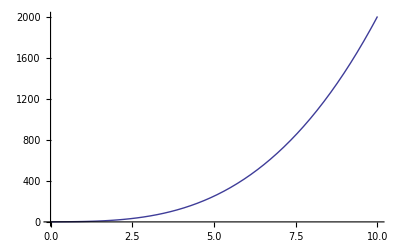

```mathematica
Plot[2 x^3+x^(1/3)+Sin[x],{x,0,10}]
```

```mathematica
D[(2 x^3+x^(1/3)+Sin[x]), x]
```

1/(3 x^(2/3))+6 x^2+Cos[x]

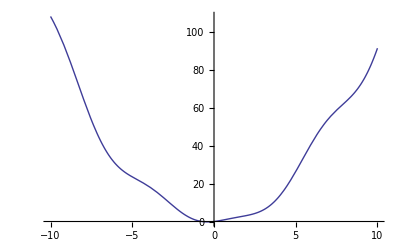

```mathematica
Plot[x Cos[x]+x^2,{x,-10,10}]
```

```mathematica
FullSimplify[(1-Sin[x])/(1+Cos[x])]
```

(1-Sin[x])/(1+Cos[x])

```mathematica
D[(1-Sin[x])/(1+Cos[x]), x]
```

-Cos[x]/(1+Cos[x])+((1-Sin[x]) Sin[x])/(1+Cos[x])^2

```mathematica
ParametricPlot3D[{t,(√3(Sin[100 π t-(2π)/3]-Sin[100 π t-π/3]))/(2π),(2Sin[100 π t]-Sin[100 π t-(2π)/3]-Sin[100 π t-π/3])/(2π)},{t,0,0.1},PlotPoints->500]
```

-Graphics3D-

```mathematica
Play[Sin[700t+25t*Sin[350t]],{t,0,3}]
```

-Graphics-

```mathematica
Play[Sin[Tan[Sinh[Cos[t]]]],{t,0,10}]
```

-Graphics-

```mathematica
Play[{t^Sin[Tan[Cot[Cosh[t]]]],Sin[700t+25t*Sin[350t]]},{t,0,10}]
```

-Graphics-

```mathematica
Plot3D[x^Sin[Tan[Cot[Cosh[x]]]]+Sin[700y+25y*Sin[350y]],{x,0,3},{y,0,0.03},Mesh->False,Lighting->Automatic]
```

-Graphics3D-

```mathematica
ContourPlot[x^Sin[Tan[Cot[Cosh[x]]]]+Sin[700 y+25 y Sin[350 y]],{x,0,3},{y,0,0.1}]
```

-Graphics-

```mathematica
Plot3D[(∫_-x^x Exp[-t^2]ⅆt)/y,{x,-100,100},{y,-100,100}, Mesh -> False]
```

-Graphics3D-

```mathematica
Animate[Plot3D[(∫_-x^x Exp[-s^2]ⅆs)/t,{x,-100,100},{y,-100,100},Mesh->False],{t,1,50}]
```

```mathematica
Show[GraphicsGrid[Partition[Table[Plot3D[x^Sin[Tan[Cot[Cosh[x]]]]+t*Sin[700y+25y*Sin[350y]],{x,0,10},{y,0,10},Mesh->False,DisplayFunction->Identity,SphericalRegion->True],{t,1,50}],3]]]
```

```mathematica
<<Calculus 'VectorAnalysie'
```

Get::noopen: Cannot open TraditionalForm`"Calculus".

VectorAnalysie' $Failed'

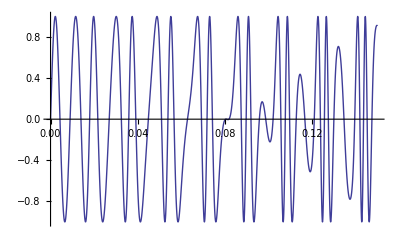

```mathematica
Plot[Sin[700t+25t*Sin[350t]],{t,0,0.15}]
```

```mathematica
TelephoneNumberOfChao1:=8881801
```

```mathematica
TelephoneNumberOfChao2:=8881802
```

```mathematica
Play[801 t^802,{t,0,4}]
```

-Graphics-

```mathematica
13076217101
```

13076217101

```mathematica
Plot3D[Sin[x-y  x],{x,-10,10},{y,-10,10},Mesh->False]
```

-Graphics3D-

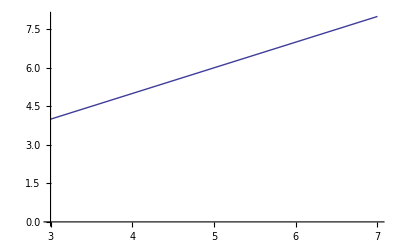

```mathematica
ListPlot[({{3, 4}, {5, 6}, {7, 8}}),PlotJoined->True,PlotRange->{0,8}]
```

```mathematica
Fit[({{3, 4}, {5, 6}, {7, 8}}),{1,x,√x,x^2,x^3,x^-1,x^4,x^5},x]
```

1.32731-0.000060064 x^5-1.84731×10^-7 x^4+0.00335976 x^3+0.0442193 x^2+0.34426 x+0.76389 √x-0.471797/x

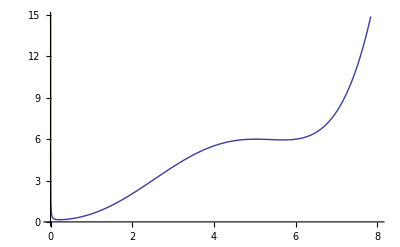

```mathematica
Plot[0.036552037823822964+0.013573160206985086/x+0.05838794299013042 √x+0.09076095418503743 x+0.19140144901780048 x^2+0.2649579596303875 x^3-0.08523329637900837 x^4+0.006637567426321268 x^5,{x,0,8}]
```

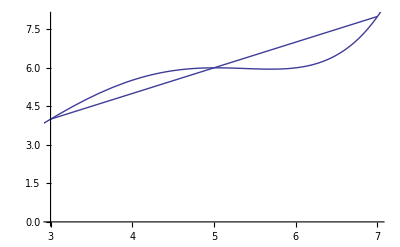

```mathematica
Show[{ListPlot[({{3, 4}, {5, 6}, {7, 8}}),PlotJoined->True,PlotRange->{0,8}],Plot[0.036552037823822964+0.013573160206985086/x+0.05838794299013042 √x+0.09076095418503743 x+0.19140144901780048 x^2+0.2649579596303875 x^3-0.08523329637900837 x^4+0.006637567426321268 x^5,{x,0,8}]}]
```

```mathematica
5*Sin[Pi/2]-3*Sin[3Pi/2]+10*Cos[Pi]
```

-2

```mathematica
Cos[Pi/3]-Tan[Pi/4]+3/4*Tan[Pi/6]^2-Sin[Pi/6]+Cos[Pi/6]^2+Sin[3Pi/2]
```

-1

```mathematica
Sin[Pi/4]^4-Cos[Pi/2]^2+6*Tan[Pi/4]^3
```

25/4

```mathematica
Clear[r,θ,t,G,M]
```

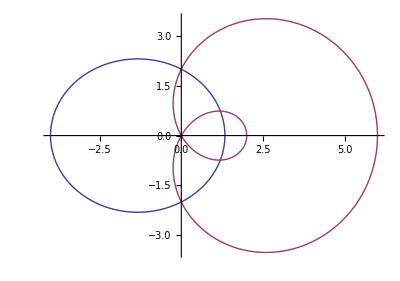

```mathematica
PolarPlot[{4/(2+Cos[t]),4 Cos[t]-2},{t,0,2 Pi}]
```

```mathematica
x=rcos theta
```

```mathematica
G=6.67*10^-11
M=6*10^24
Subscript[v, 0]=100
PolarPlot[{((3*√2*G*M)/4)^(2/3)t^(2/3)Cos[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]],((3*√2*G*M)/4)^(2/3)t^(2/3)*Sin[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]]},{t,0,100}]
```

6.67×10^-11

6000000000000000000000000

100

-Graphics-

```mathematica
G=6.67*10^-11
M=6*10^24
Subscript[v, 0]=1000
PolarPlot[{((3*√2*G*M)/4)^(2/3)t^(2/3)Cos[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]],((3*√2*G*M)/4)^(2/3)t^(2/3)*Sin[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]]},{t,0,700}]
```

6.67×10^-11

6000000000000000000000000

1000

-Graphics-

6.67×10^-11

6000000000000000000000000

300000000

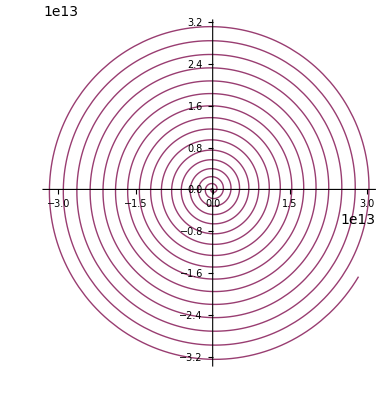

```mathematica
G=6.67*10^-11
M=6*10^24
Subscript[v, 0]=300000000
PolarPlot[{((3*√2*G*M)/4)^(2/3)t^(2/3)Cos[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]],((3*√2*G*M)/4)^(2/3)t^(2/3)*Sin[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]]},{t,0,100}]
```

6.67×10^-11

6000000000000000000000000

10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

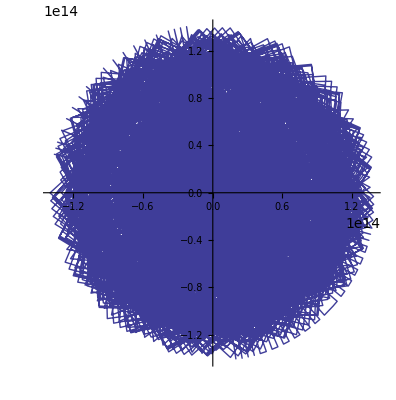

```mathematica
G=6.67*10^-11
M=6*10^24
Subscript[v, 0]=10^1000
PolarPlot[{((3*√2*G*M)/4)^(2/3)t^(2/3)Cos[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]],((3*√2*G*M)/4)^(2/3)t^(2/3)*Sin[ArcSin[2/3*((3 √2*G*M)/4)^(2/3)/Subscript[v, 0]*t^(2/3)]]},{t,0,4000000}]
```

```mathematica
Clear[x, y, z]
ContourPlot3D[1/(240 √(5 π))(ⅇ^(3 (x^2+y^2+z^2)^(1/2)/2) ((x^2+y^2+z^2)^(1/2))^2 √(((x^2+y^2+z^2)^(1/2))^3) (4140+6750 (x^2+y^2+z^2)^(1/2)+3465 ((x^2+y^2+z^2)^(1/2))^2+730 ((x^2+y^2+z^2)^(1/2))^3+65 ((x^2+y^2+z^2)^(1/2))^4+2 ((x^2+y^2+z^2)^(1/2))^5) z/((x^2+y^2+z^2)^(1/2))),{x,99,101},{y,99,101},{z,99,101}]
```

-Graphics3D-